```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/2-d-data";}];
```

```mathematica
Kernel[x_?NumberQ]:=NIntegrate[ϕ3[p]/(p-x)^2,{p,0,x,1},Method->"PrincipalValue"]
```

```mathematica
Amp[ω_][ϕ1_,ϕ2_,ϕ3_]:=(1-ℂ)(1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},Method->"LocalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},Method->"LocalAdaptive"]+1/Nc 1/(1-ω)NIntegrate[ϕ3[x],{x,0,1}]NIntegrate[ϕ1[x]ϕ2[x/ω],{x,0,ω},Method->"LocalAdaptive"]);(*r1=1*)
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;Nb=29;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
accDetermineϕ[m1_,m2_,β_,Nb_]:=
Module[{psi,ϵ=10^-6,Kernel1,Kernel2,hMT,sMT,sMatrix,hMTUp,hMT1,hMatrix,eg,vals,vecs,func,μ,nfunc},
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}];
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}];
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((m1^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20];
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}];
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;hMTUp=PadLeft[#,Nb+1]&/@ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
(*Print[hMTUp];*)
hMatrix=Transpose[hMTUp]+hMTUp-DiagonalMatrix[Diagonal[hMTUp]];
(*Print[MatrixForm[hMatrix]];*)
eg[μ_]:=Det[hMatrix-μ^2*sMatrix];
μ=Sort@DeleteDuplicatesBy[Table[μ/.FindRoot[eg[μ]==0,{μ,a,a+0.2}],{a,0,Nb^2,0.2}],SetPrecision[#,2]&];
Print[μ];
vecs=(Flatten@NullSpace[hMatrix-#^2 sMatrix,Tolerance->0.001])&/@μ;
Print[vecs];Print[Dimensions@vecs];
func=ParallelTable[Table[psi[i,x],{i,0,Nb}].vecs[[j]],{j,1,Length[vecs]}];
nfunc=ParallelTable[Quiet[func[[n]]/√NIntegrate[func[[n]]^2,{x,0,1}]],{n,1,20}];
Clear[func,vecs];
{μ,nfunc}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
ω[M1_,M2_,M3_]:=(*-*)(√((M1^2+M2^2-M3^2)^2-4 M1^2 M2^2))/(2 M1^2)+M2^2/(2 M1^2)-M3^2/(2 M1^2)+1/2
```

```mathematica
ASin[n_][m1_]:=
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
Set@@{ϕ[x_],ϕx};
Export[dir<>filename,{Vals,ϕx}]
},
{
{Vals,ϕx}=Import[dir<>filename];
Set@@{ϕ[x_],ϕx};
}
];
(*Print[ϕ[y][[2]]];*)
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
(*Print[ϕ3[x]];*)
Print[ω[M1,M2,M3]];
(*Information[Amp];*)
Ares=Amp[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
]
```

```mathematica
At[n_][ma_,mb_,δm_]:=Table[
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
If[m1<0.5,
filename="/acceigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];,
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
],{m1,ma,mb,δm}]
```

```mathematica
Aall[ma_,mb_,δm_]:=Table[
Block[{ϕx,m2,Φ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow},
(*Print[Definition[Aalltable]];*)
SetSharedVariable[Aalltable];
(*SetSharedVariable[m2,m1];*)
m2=m1;
(*If[m1<0.5,
filename="/acceigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=accDetermineϕ[m1,m2,β,Nb];
Φ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx}]
},
{
{Vals,ϕx}=Import[dir<>filename];
Φ[x_]=ϕx;
}
];,*)
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
Set@@{Φ[x_],ϕx};
Export[dir<>filename,{Vals,ϕx}]
},
{
{Vals,ϕx}=Import[dir<>filename];
Set@@{Φ[x_],ϕx};
}
];
(*];*)
Print["m="<>ToString[m1]<>": Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M2,ϕ2}={Mn[#][Vals],ϕn[#][Φ]}&[1];
{M3,ϕ3}={Mn[#][Vals],ϕn[#][Φ]}&[1];
ParallelTable[
{M1,ϕ1}={Mn[#][Vals],ϕn[#][Φ]}&[n];
ωnow=ω[M1,M2,M3];
Print["m="<>ToString[m1]<>", ω="<>ToString[ωnow]<>", n="<>ToString[n]];
If[ωnow∈Reals,{
Ares=Amp[ωnow][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
AppendTo[Aalltable[[n]],{m1^2,Ares}](*Output to variable `Aalltable`*)},]
,{n,5,17,1}]
],{m1,ma,mb,δm}]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

```mathematica
ParallelEvaluate[Information[ϕn]]
```

```mathematica
Aalltable=Table[{},{n,1,18}];
```

```mathematica
ASin[5][0.5]
```

```mathematica
Aall[0.2,1.5,0.02](* Aall[minimal mass,maximal mass,mass inteval] *)
```

m=0.2: Wavefunction build complete.

m=0.2, ω=0.77983, n=5

m=0.2, ω=0.861123, n=7

m=0.2, ω=0.898064, n=9

m=0.2, ω=0.919432, n=11

m=0.2, ω=0.933393, n=13

m=0.2, ω=0.943235, n=15

m=0.2, ω=0.947143, n=16

m=0.2, ω=0.950548, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.919375}. NIntegrate obtained -0.0000183226 and 6.06983×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.919379}. NIntegrate obtained -0.0000201613 and 6.68383×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.919382}. NIntegrate obtained -0.0000222214 and 7.37411×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.943181}. NIntegrate obtained -9.3095×10^-6 and 3.07891×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.943184}. NIntegrate obtained -0.0000102623 and 3.39685×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.943188}. NIntegrate obtained -0.0000113544 and 3.76277×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.933325}. NIntegrate obtained 9.03655×10^-6 and 2.98641×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.933328}. NIntegrate obtained 9.94726×10^-6 and 3.28822×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.861057}. NIntegrate obtained -0.0000392666 and 1.30512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.933332}. NIntegrate obtained 0.000010943 and 3.61864×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.86106}. NIntegrate obtained -0.0000432494 and 1.43821×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.861064}. NIntegrate obtained -0.0000476021 and 1.5839×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.950479}. NIntegrate obtained 4.9385×10^-6 and 1.6299×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.950483}. NIntegrate obtained 5.43651×10^-6 and 1.79459×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.950486}. NIntegrate obtained 5.98111×10^-6 and 1.97488×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.947066}. NIntegrate obtained 4.69367×10^-6 and 1.54912×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.94707}. NIntegrate obtained 5.17425×10^-6 and 1.70792×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.947074}. NIntegrate obtained 5.70079×10^-6 and 1.88199×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.897991}. NIntegrate obtained -0.0000185501 and 6.14452×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.897995}. NIntegrate obtained -0.0000204453 and 6.77421×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.897998}. NIntegrate obtained -0.000022521 and 7.4645×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.779761}. NIntegrate obtained 0.0000730862 and 2.44325×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.779764}. NIntegrate obtained 0.0000805526 and 2.69458×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.779767}. NIntegrate obtained 0.0000887813 and 2.97196×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.04,-3.11394}

m=0.2, ω=0.830057, n=6

{0.04,2.2391}

m=0.2, ω=0.882453, n=8

{0.04,1.85921}

m=0.2, ω=0.91, n=10

{0.04,1.70541}

m=0.2, ω=0.927074, n=12

{0.04,-1.52622}

m=0.2, ω=0.938706, n=14

{0.04,1.55502}

{0.04,-1.50351}

{0.04,-1.40151}

{0.04,-2.52306}

{0.04,1.979}

{0.04,1.76705}

{0.04,1.60874}

{0.04,-1.51448}

m=0.22: Wavefunction build complete.

m=0.22, ω=0.772861, n=5

m=0.22, ω=0.857075, n=7

m=0.22, ω=0.895136, n=9

m=0.22, ω=0.917125, n=11

m=0.22, ω=0.931486, n=13

m=0.22, ω=0.941609, n=15

m=0.22, ω=0.945628, n=16

m=0.22, ω=0.94913, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.917075}. NIntegrate obtained 0.000018243 and 6.04497×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.917079}. NIntegrate obtained 0.0000201922 and 6.70014×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.917082}. NIntegrate obtained 0.0000225026 and 7.4811×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.931425}. NIntegrate obtained -9.16841×10^-6 and 3.02707×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.931429}. NIntegrate obtained -0.0000100868 and 3.33191×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.931433}. NIntegrate obtained -0.0000111043 and 3.67044×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.857012}. NIntegrate obtained 0.0000359697 and 1.19449×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.857015}. NIntegrate obtained 0.0000395756 and 1.31505×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.857019}. NIntegrate obtained 0.0000435237 and 1.44732×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.89507}. NIntegrate obtained 0.0000185387 and 6.13532×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.895074}. NIntegrate obtained 0.0000203994 and 6.75405×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.895077}. NIntegrate obtained 0.0000224373 and 7.43281×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.945559}. NIntegrate obtained 4.63908×10^-6 and 1.52897×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.941533}. NIntegrate obtained -4.5924×10^-6 and 1.51359×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.945563}. NIntegrate obtained 5.10555×10^-6 and 1.68307×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.941537}. NIntegrate obtained -5.05901×10^-6 and 1.66761×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.945566}. NIntegrate obtained 5.61667×10^-6 and 1.85211×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.941541}. NIntegrate obtained -5.57088×10^-6 and 1.83665×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.772802}. NIntegrate obtained -0.0000780717 and 2.61289×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.772805}. NIntegrate obtained -0.0000859203 and 2.8783×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.772808}. NIntegrate obtained -0.000094505 and 3.16934×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.949039}. NIntegrate obtained 2.26984×10^-6 and 7.47492×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.949043}. NIntegrate obtained 2.49636×10^-6 and 8.22145×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.949047}. NIntegrate obtained 2.74843×10^-6 and 9.05224×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0484,3.4099}

m=0.22, ω=0.824991, n=6

{0.0484,-2.41547}

m=0.22, ω=0.879061, n=8

{0.0484,-2.02597}

m=0.22, ω=0.907421, n=10

{0.0484,-1.82612}

m=0.22, ω=0.924986, n=12

{0.0484,1.80822}

m=0.22, ω=0.936951, n=14

{0.0484,-1.61631}

{0.0484,1.66911}

{0.0484,2.74119}

{0.0484,-1.65231}

{0.0484,2.19802}

{0.0484,2.01596}

{0.0484,-1.86648}

{0.0484,-1.71364}

m=0.24: Wavefunction build complete.

m=0.24, ω=0.765859, n=5

m=0.24, ω=0.85305, n=7

m=0.24, ω=0.892229, n=9

m=0.24, ω=0.914837, n=11

m=0.24, ω=0.929595, n=13

m=0.24, ω=0.939996, n=15

m=0.24, ω=0.944125, n=16

m=0.24, ω=0.947724, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.914794}. NIntegrate obtained -0.0000189004 and 6.27336×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.914798}. NIntegrate obtained -0.0000213198 and 7.09524×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.914801}. NIntegrate obtained -0.0000244676 and 8.17293×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.852997}. NIntegrate obtained -0.0000393157 and 1.30669×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.853}. NIntegrate obtained -0.0000432705 and 1.43984×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.853004}. NIntegrate obtained -0.0000477188 and 1.59025×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.929541}. NIntegrate obtained -9.50533×10^-6 and 3.13654×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.929545}. NIntegrate obtained -0.0000104874 and 3.46381×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.929549}. NIntegrate obtained -0.0000116173 and 3.84189×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.944064}. NIntegrate obtained 4.85597×10^-6 and 1.59843×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.944067}. NIntegrate obtained 5.34296×10^-6 and 1.75948×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.944071}. NIntegrate obtained 5.88387×10^-6 and 1.93875×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.939931}. NIntegrate obtained -4.97568×10^-6 and 1.63788×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.939935}. NIntegrate obtained -5.47309×10^-6 and 1.80221×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.939939}. NIntegrate obtained -6.02115×10^-6 and 1.98356×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.892171}. NIntegrate obtained 0.0000185892 and 6.14806×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.892174}. NIntegrate obtained 0.0000204483 and 6.76775×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.892178}. NIntegrate obtained 0.000022512 and 7.45761×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.765806}. NIntegrate obtained 0.0000747877 and 2.50544×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.765809}. NIntegrate obtained 0.0000822005 and 2.75744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.765812}. NIntegrate obtained 0.0000903527 and 3.03566×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.94764}. NIntegrate obtained 2.38202×10^-6 and 7.83068×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.947644}. NIntegrate obtained 2.62094×10^-6 and 8.61687×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.947647}. NIntegrate obtained 2.88482×10^-6 and 9.48537×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0576,-3.55861}

m=0.24, ω=0.81994, n=6

{0.0576,2.59214}

m=0.24, ω=0.875691, n=8

{0.0576,2.06263}

m=0.24, ω=0.922916, n=12

{0.0576,1.85863}

m=0.24, ω=0.93521, n=14

{0.0576,-2.2547}

m=0.24, ω=0.904862, n=10

{0.0576,-1.78071}

{0.0576,1.77849}

{0.0576,-2.95086}

{0.0576,2.4168}

{0.0576,-1.68899}

{0.0576,2.10541}

{0.0576,1.90705}

{0.0576,-1.85037}

m=0.26: Wavefunction build complete.

m=0.26, ω=0.758813, n=5

m=0.26, ω=0.849046, n=7

m=0.26, ω=0.889344, n=9

m=0.26, ω=0.912566, n=11

m=0.26, ω=0.927719, n=13

m=0.26, ω=0.938396, n=15

m=0.26, ω=0.942634, n=16

m=0.26, ω=0.946328, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.912527}. NIntegrate obtained -0.0000180667 and 6.00174×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.91253}. NIntegrate obtained -0.0000207418 and 6.91561×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.912534}. NIntegrate obtained -0.0000244131 and 8.18073×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.927672}. NIntegrate obtained 9.4253×10^-6 and 3.11125×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.927676}. NIntegrate obtained 0.0000105217 and 3.47935×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.927679}. NIntegrate obtained 0.0000118777 and 3.93748×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.889293}. NIntegrate obtained -0.0000189604 and 6.27015×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.889296}. NIntegrate obtained -0.0000209274 and 6.92905×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.889299}. NIntegrate obtained -0.0000231938 and 7.6918×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.849}. NIntegrate obtained 0.00003888 and 1.29369×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.849003}. NIntegrate obtained 0.0000430733 and 1.43605×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.849006}. NIntegrate obtained 0.0000480503 and 1.60612×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.94258}. NIntegrate obtained 4.78022×10^-6 and 1.57208×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.942583}. NIntegrate obtained 5.27707×10^-6 and 1.73694×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.942587}. NIntegrate obtained 5.84991×10^-6 and 1.92774×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.938335}. NIntegrate obtained -4.6754×10^-6 and 1.53658×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.938338}. NIntegrate obtained -5.14462×10^-6 and 1.69157×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.938342}. NIntegrate obtained -5.66704×10^-6 and 1.86452×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.946252}. NIntegrate obtained 2.34774×10^-6 and 7.70397×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.946255}. NIntegrate obtained 2.58261×10^-6 and 8.47587×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.946259}. NIntegrate obtained 2.84096×10^-6 and 9.3254×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.758746}. NIntegrate obtained -0.000037327 and 1.24303×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.758749}. NIntegrate obtained -0.0000410082 and 1.36666×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.758752}. NIntegrate obtained -0.0000450725 and 1.50337×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0676,-2.77104}

m=0.26, ω=0.872344, n=8

{0.0676,3.749}

m=0.26, ω=0.814901, n=6

{0.0676,2.14226}

m=0.26, ω=0.920861, n=12

{0.0676,2.40715}

m=0.26, ω=0.902322, n=10

{0.0676,-2.01428}

m=0.26, ω=0.933483, n=14

{0.0676,-1.8544}

{0.0676,1.93347}

{0.0676,2.5856}

{0.0676,-1.87151}

{0.0676,-3.14388}

{0.0676,-2.22435}

{0.0676,2.08449}

{0.0676,1.9354}

m=0.28: Wavefunction build complete.

m=0.28, ω=0.751704, n=5

m=0.28, ω=0.845056, n=7

m=0.28, ω=0.886475, n=9

m=0.28, ω=0.910309, n=11

m=0.28, ω=0.925854, n=13

m=0.28, ω=0.936806, n=15

m=0.28, ω=0.941153, n=16

m=0.28, ω=0.944941, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.845017}. NIntegrate obtained -0.0000390187 and 1.30209×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.84502}. NIntegrate obtained -0.0000440424 and 1.47477×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.845023}. NIntegrate obtained -0.0000505469 and 1.70031×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.910277}. NIntegrate obtained -0.0000198154 and 6.62625×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.910281}. NIntegrate obtained -0.0000241269 and 8.12299×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.910284}. NIntegrate obtained -0.0000307416 and 1.04461×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.925815}. NIntegrate obtained 0.0000100977 and 3.34063×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.925819}. NIntegrate obtained 0.0000116008 and 3.85096×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.925822}. NIntegrate obtained 0.0000136566 and 4.5548×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.886431}. NIntegrate obtained -0.0000191395 and 6.33545×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.886434}. NIntegrate obtained -0.0000213746 and 7.09059×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.886437}. NIntegrate obtained -0.0000241366 and 8.03015×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.936752}. NIntegrate obtained -4.60834×10^-6 and 1.51307×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.936756}. NIntegrate obtained -5.08977×10^-6 and 1.6726×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.936759}. NIntegrate obtained -5.64591×10^-6 and 1.8576×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.941106}. NIntegrate obtained 4.96763×10^-6 and 1.63363×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.941109}. NIntegrate obtained 5.55059×10^-6 and 1.82833×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.941113}. NIntegrate obtained 6.27156×10^-6 and 2.07055×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.751646}. NIntegrate obtained -0.0000378265 and 1.26104×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.751649}. NIntegrate obtained -0.000041555 and 1.38686×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.751652}. NIntegrate obtained -0.0000456531 and 1.52554×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.944872}. NIntegrate obtained 2.4097×10^-6 and 7.89282×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.944876}. NIntegrate obtained 2.6492×10^-6 and 8.67941×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.94488}. NIntegrate obtained 2.91321×10^-6 and 9.54749×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0784,2.9456}

m=0.28, ω=0.869013, n=8

{0.0784,3.94464}

m=0.28, ω=0.809865, n=6

{0.0784,2.50354}

m=0.28, ω=0.899797, n=10

{0.0784,2.26809}

m=0.28, ω=0.91882, n=12

{0.0784,-2.13991}

m=0.28, ω=0.931767, n=14

{0.0784,-1.99704}

{0.0784,2.0032}

{0.0784,3.31855}

{0.0784,-1.91878}

{0.0784,2.70337}

{0.0784,-2.40945}

{0.0784,2.20869}

{0.0784,-2.09587}

m=0.3: Wavefunction build complete.

m=0.3, ω=0.744507, n=5

m=0.3, ω=0.841072, n=7

m=0.3, ω=0.883616, n=9

m=0.3, ω=0.908062, n=11

m=0.3, ω=0.923998, n=13

m=0.3, ω=0.935223, n=15

m=0.3, ω=0.939678, n=16

m=0.3, ω=0.943561, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.908034}. NIntegrate obtained 0.000020123 and 6.75912×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.908037}. NIntegrate obtained 0.0000255872 and 8.67321×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.908041}. NIntegrate obtained 0.0000344312 and 1.18176×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.883579}. NIntegrate obtained -0.000019533 and 6.4854×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.883582}. NIntegrate obtained -0.0000224387 and 7.47938×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.883585}. NIntegrate obtained -0.0000263964 and 8.84542×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.841036}. NIntegrate obtained 0.0000357412 and 1.19466×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.841039}. NIntegrate obtained 0.0000410377 and 1.37796×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.841042}. NIntegrate obtained 0.0000482466 and 1.6299×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.939638}. NIntegrate obtained 5.09872×10^-6 and 1.67953×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.939642}. NIntegrate obtained 5.86074×10^-6 and 1.93664×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.939646}. NIntegrate obtained 6.89956×10^-6 and 2.28993×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.923963}. NIntegrate obtained -9.43773×10^-6 and 3.1259×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.923966}. NIntegrate obtained -0.0000111083 and 3.69629×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.92397}. NIntegrate obtained -0.0000135157 and 4.52603×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.935176}. NIntegrate obtained 4.74398×10^-6 and 1.55741×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.93518}. NIntegrate obtained 5.30449×10^-6 and 1.74433×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.935184}. NIntegrate obtained 5.99745×10^-6 and 1.97677×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.943499}. NIntegrate obtained -2.3691×10^-6 and 7.74665×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.943503}. NIntegrate obtained -2.60729×10^-6 and 8.52937×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.943506}. NIntegrate obtained -2.87384×10^-6 and 9.40706×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.744438}. NIntegrate obtained 0.0000195317 and 6.47789×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.744441}. NIntegrate obtained 0.0000213867 and 7.0986×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.744444}. NIntegrate obtained 0.000023443 and 7.78769×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.09,-3.10793}

m=0.3, ω=0.865692, n=8

{0.09,-4.05677}

m=0.3, ω=0.804818, n=6

{0.09,-2.42061}

m=0.3, ω=0.916787, n=12

{0.09,2.64242}

m=0.3, ω=0.897282, n=10

{0.09,2.22262}

m=0.3, ω=0.930058, n=14

{0.09,-2.06825}

{0.09,-2.14195}

{0.09,2.0625}

{0.09,-2.82292}

{0.09,3.47503}

{0.09,-2.51028}

{0.09,-2.29372}

{0.09,-2.15608}

m=0.32: Wavefunction build complete.

m=0.32, ω=0.737194, n=5

m=0.32, ω=0.837083, n=7

m=0.32, ω=0.880761, n=9

m=0.32, ω=0.905819, n=11

m=0.32, ω=0.922146, n=13

m=0.32, ω=0.933644, n=15

m=0.32, ω=0.938207, n=16

m=0.32, ω=0.942183, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.905795}. NIntegrate obtained -0.0000210111 and 7.10326×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.905798}. NIntegrate obtained -0.0000281715 and 9.64227×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.905802}. NIntegrate obtained -0.0000404589 and 1.4091×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.922114}. NIntegrate obtained -9.25761×10^-6 and 3.07287×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.922118}. NIntegrate obtained -0.0000112541 and 3.75899×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.922121}. NIntegrate obtained -0.0000142843 and 4.8121×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.880727}. NIntegrate obtained 0.0000184447 and 6.13454×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.88073}. NIntegrate obtained 0.0000216966 and 7.2541×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.880734}. NIntegrate obtained 0.0000263566 and 8.87504×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.933604}. NIntegrate obtained -4.89191×10^-6 and 1.60851×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.933608}. NIntegrate obtained -5.62509×10^-6 and 1.85544×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.933612}. NIntegrate obtained -6.62104×10^-6 and 2.19352×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.837035}. NIntegrate obtained -0.0000186912 and 6.17462×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.837038}. NIntegrate obtained -0.000020653 and 6.83391×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.837041}. NIntegrate obtained -0.0000229253 and 7.60147×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.938149}. NIntegrate obtained 2.50211×10^-6 and 8.16847×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.938153}. NIntegrate obtained 2.7585×10^-6 and 9.01131×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.938156}. NIntegrate obtained 3.04998×10^-6 and 9.97217×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.942104}. NIntegrate obtained 1.23971×10^-6 and 4.03897×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.942107}. NIntegrate obtained 1.35938×10^-6 and 4.42954×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.942111}. NIntegrate obtained 1.49166×10^-6 and 4.86148×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.737073}. NIntegrate obtained 4.64002×10^-6 and 1.52094×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.737076}. NIntegrate obtained 4.80021×10^-6 and 1.57398×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.737079}. NIntegrate obtained 4.97475×10^-6 and 1.6318×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1024,3.24941}

m=0.32, ω=0.862372, n=8

{0.1024,-2.7889}

m=0.32, ω=0.894772, n=10

{0.1024,2.49602}

m=0.32, ω=0.914759, n=12

{0.1024,2.35668}

m=0.32, ω=0.928354, n=14

{0.1024,2.20613}

{0.1024,-4.15835}

m=0.32, ω=0.799748, n=6

{0.1024,-2.18005}

{0.1024,2.96508}

{0.1024,2.6143}

{0.1024,-2.1109}

{0.1024,2.43501}

{0.1024,-2.29364}

{0.1024,-3.61436}

m=0.34: Wavefunction build complete.

m=0.34, ω=0.729737, n=5

m=0.34, ω=0.833081, n=7

m=0.34, ω=0.877903, n=9

m=0.34, ω=0.903576, n=11

m=0.34, ω=0.920295, n=13

m=0.34, ω=0.932065, n=15

m=0.34, ω=0.936736, n=16

m=0.34, ω=0.940806, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.877876}. NIntegrate obtained -0.0000216564 and 7.27409×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.877879}. NIntegrate obtained -0.0000274015 and 9.29216×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.877882}. NIntegrate obtained -0.0000365852 and 1.25705×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.903541}. NIntegrate obtained -9.39855×10^-6 and 3.10555×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.903545}. NIntegrate obtained -0.0000110578 and 3.67121×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.903548}. NIntegrate obtained -0.0000134251 and 4.48616×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.920266}. NIntegrate obtained 9.20857×10^-6 and 3.06729×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.920269}. NIntegrate obtained 0.0000116618 and 3.91727×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.920273}. NIntegrate obtained 0.0000155887 and 5.29757×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.932029}. NIntegrate obtained 4.68715×10^-6 and 1.54204×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.932033}. NIntegrate obtained 5.51688×10^-6 and 1.82282×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.932036}. NIntegrate obtained 6.70136×10^-6 and 2.2273×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.833039}. NIntegrate obtained 0.0000184705 and 6.11129×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.833042}. NIntegrate obtained 0.0000206638 and 6.85527×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.833045}. NIntegrate obtained 0.0000233699 and 7.77993×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.936685}. NIntegrate obtained 2.47066×10^-6 and 8.05747×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.936689}. NIntegrate obtained 2.74601×10^-6 and 8.96605×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.936693}. NIntegrate obtained 3.07463×10^-6 and 1.00552×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.940734}. NIntegrate obtained -1.21929×10^-6 and 3.96332×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.940738}. NIntegrate obtained -1.33805×10^-6 and 4.35039×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.940741}. NIntegrate obtained -1.46948×10^-6 and 4.7791×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.729667}. NIntegrate obtained -9.4592×10^-6 and 3.12253×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.72967}. NIntegrate obtained -0.0000103153 and 3.40782×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.729672}. NIntegrate obtained -0.0000112672 and 3.72549×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1156,2.88713}

m=0.34, ω=0.89226, n=10

{0.1156,-3.36843}

m=0.34, ω=0.859046, n=8

{0.1156,2.62027}

m=0.34, ω=0.912731, n=12

{0.1156,4.24857}

m=0.34, ω=0.794641, n=6

{0.1156,-2.42205}

m=0.34, ω=0.926649, n=14

{0.1156,-2.3195}

{0.1156,-2.25303}

{0.1156,2.22786}

{0.1156,2.74692}

{0.1156,-3.09806}

{0.1156,3.73566}

{0.1156,-2.50438}

{0.1156,-2.35323}

m=0.36: Wavefunction build complete.

m=0.36, ω=0.722103, n=5

m=0.36, ω=0.829055, n=7

m=0.36, ω=0.875037, n=9

m=0.36, ω=0.901328, n=11

m=0.36, ω=0.918439, n=13

m=0.36, ω=0.930484, n=15

m=0.36, ω=0.935263, n=16

m=0.36, ω=0.939427, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.875013}. NIntegrate obtained 0.0000219822 and 7.43386×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.875016}. NIntegrate obtained 0.0000292461 and 1.002×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.875019}. NIntegrate obtained 0.0000415566 and 1.45035×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.918414}. NIntegrate obtained 9.54012×10^-6 and 3.19491×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.918418}. NIntegrate obtained 0.0000127096 and 4.30546×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.918421}. NIntegrate obtained 0.000018092 and 6.22989×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.930455}. NIntegrate obtained -5.45454×10^-6 and 1.80754×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.930458}. NIntegrate obtained -6.89484×10^-6 and 2.30311×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.930462}. NIntegrate obtained -9.18779×10^-6 and 3.10318×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.901297}. NIntegrate obtained 9.15793×10^-6 and 3.03225×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.9013}. NIntegrate obtained 0.0000111075 and 3.7013×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.901304}. NIntegrate obtained 0.0000140324 and 4.71694×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.82902}. NIntegrate obtained 0.0000186769 and 6.20367×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.829023}. NIntegrate obtained 0.0000214674 and 7.163×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.829026}. NIntegrate obtained 0.0000252253 and 8.46759×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.722081}. NIntegrate obtained -0.0000392275 and 1.36512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.722083}. NIntegrate obtained -0.0000493216 and 1.74158×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.722086}. NIntegrate obtained -0.0000652658 and 2.3506×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.935216}. NIntegrate obtained 2.29058×10^-6 and 7.45885×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.935219}. NIntegrate obtained 2.56649×10^-6 and 8.3707×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.935223}. NIntegrate obtained 2.90733×10^-6 and 9.50317×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.939333}. NIntegrate obtained 5.94008×10^-7 and 1.9235×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.939337}. NIntegrate obtained 6.45847×10^-7 and 2.09166×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.93934}. NIntegrate obtained 7.03663×10^-7 and 2.27924×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1296,4.27308}

m=0.36, ω=0.789484, n=6

{0.1296,-3.47026}

m=0.36, ω=0.855708, n=8

{0.1296,-2.98395}

m=0.36, ω=0.889743, n=10

{0.1296,-2.53462}

m=0.36, ω=0.924942, n=14

{0.1296,-2.71222}

m=0.36, ω=0.910699, n=12

{0.1296,2.38225}

{0.1296,-2.33894}

{0.1296,-3.19994}

{0.1296,-2.83159}

{0.1296,-3.8382}

{0.1296,2.61624}

{0.1296,-2.27713}

{0.1296,2.46358}

m=0.38: Wavefunction build complete.

m=0.38, ω=0.71426, n=5

m=0.38, ω=0.825, n=7

m=0.38, ω=0.872157, n=9

m=0.38, ω=0.899072, n=11

m=0.38, ω=0.916578, n=13

m=0.38, ω=0.928897, n=15

m=0.38, ω=0.933784, n=16

m=0.38, ω=0.938043, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.916556}. NIntegrate obtained -0.0000103723 and 3.50196×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.916559}. NIntegrate obtained -0.0000146936 and 5.04207×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.916563}. NIntegrate obtained -0.0000225893 and 7.94581×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.872133}. NIntegrate obtained 0.0000176932 and 5.96615×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.872136}. NIntegrate obtained 0.0000234595 and 8.01336×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.87214}. NIntegrate obtained 0.0000331759 and 1.1543×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.899047}. NIntegrate obtained 0.0000112965 and 3.78563×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.899051}. NIntegrate obtained 0.0000149895 and 5.08349×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.899054}. NIntegrate obtained 0.0000212202 and 7.32039×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.928868}. NIntegrate obtained -4.51156×10^-6 and 1.49043×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.928871}. NIntegrate obtained -5.69134×10^-6 and 1.89495×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.928875}. NIntegrate obtained -7.55871×10^-6 and 2.54429×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.933744}. NIntegrate obtained 2.35655×10^-6 and 7.68062×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.933748}. NIntegrate obtained 2.71296×10^-6 and 8.86847×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.933751}. NIntegrate obtained 3.19226×10^-6 and 1.04777×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.714243}. NIntegrate obtained 0.0000400109 and 1.44004×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.714246}. NIntegrate obtained 0.0000561492 and 2.07855×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.714249}. NIntegrate obtained 0.0000851568 and 3.28852×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.824952}. NIntegrate obtained 9.45898×10^-6 and 3.10279×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.824955}. NIntegrate obtained 0.0000104639 and 3.43844×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.824958}. NIntegrate obtained 0.000011634 and 3.83118×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.937924}. NIntegrate obtained 2.9837×10^-7 and 9.62209×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.937928}. NIntegrate obtained 3.1728×10^-7 and 1.02336×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.937931}. NIntegrate obtained 3.38534×10^-7 and 1.09208×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1444,-4.27213}

m=0.38, ω=0.784265, n=6

{0.1444,-3.09224}

m=0.38, ω=0.887214, n=10

{0.1444,-2.79313}

m=0.38, ω=0.908659, n=12

{0.1444,-3.56122}

m=0.38, ω=0.85235, n=8

{0.1444,2.59542}

m=0.38, ω=0.923229, n=14

{0.1444,2.47282}

{0.1444,-2.41003}

{0.1444,-2.92394}

{0.1444,2.69073}

{0.1444,3.28839}

{0.1444,-2.52257}

{0.1444,-2.36913}

{0.1444,-3.92118}

m=0.4: Wavefunction build complete.

m=0.4, ω=0.706171, n=5

m=0.4, ω=0.820907, n=7

m=0.4, ω=0.869259, n=9

m=0.4, ω=0.896803, n=11

m=0.4, ω=0.914706, n=13

m=0.4, ω=0.927302, n=15

m=0.4, ω=0.932298, n=16

m=0.4, ω=0.936652, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.914689}. NIntegrate obtained 0.0000118113 and 4.03845×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.914692}. NIntegrate obtained 0.0000180539 and 6.32698×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.914695}. NIntegrate obtained 0.0000306966 and 1.1226×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.896779}. NIntegrate obtained -9.19595×10^-6 and 3.07183×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.896782}. NIntegrate obtained -0.0000121615 and 4.11066×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.896786}. NIntegrate obtained -0.0000171363 and 5.89112×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.706163}. NIntegrate obtained 0.0000651478 and 2.70491×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.706166}. NIntegrate obtained 0.00012466 and 5.99187×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.706168}. NIntegrate obtained 0.000305997 and 2.22404×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.869229}. NIntegrate obtained 9.41983×10^-6 and 3.11637×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.869232}. NIntegrate obtained 0.0000113969 and 3.79613×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.869235}. NIntegrate obtained 0.0000143287 and 4.81703×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.927266}. NIntegrate obtained 2.57196×10^-6 and 8.38789×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.927269}. NIntegrate obtained 3.02551×10^-6 and 9.90722×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.927273}. NIntegrate obtained 3.66409×10^-6 and 1.20653×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.820866}. NIntegrate obtained 9.08196×10^-6 and 2.98308×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.820869}. NIntegrate obtained 0.0000101779 and 3.35228×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.820872}. NIntegrate obtained 0.0000115287 and 3.81055×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.932245}. NIntegrate obtained 1.24703×10^-6 and 4.02845×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.932248}. NIntegrate obtained 1.38101×10^-6 and 4.46532×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.932252}. NIntegrate obtained 1.53747×10^-6 and 4.97715×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.16,-4.22677}

m=0.4, ω=0.778973, n=6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.936409}. NIntegrate obtained -7.29467×10^-8 and 2.33922×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.936412}. NIntegrate obtained -7.52373×10^-8 and 2.4127×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.936416}. NIntegrate obtained -7.76135×10^-8 and 2.48893×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.16,2.88517}

m=0.4, ω=0.906609, n=12

{0.16,-3.17572}

m=0.4, ω=0.884672, n=10

{0.16,-3.64315}

m=0.4, ω=0.848968, n=8

{0.16,-2.68611}

m=0.4, ω=0.921507, n=14

{0.16,-2.53159}

{0.16,-3.98391}

{0.16,-2.47606}

{0.16,-3.3784}

{0.16,-2.77143}

{0.16,3.0163}

{0.16,-2.60963}

{0.16,2.41931}

m=0.42: Wavefunction build complete.

m=0.42, ω=0.697797, n=5

m=0.42, ω=0.81677, n=7

m=0.42, ω=0.86634, n=9

m=0.42, ω=0.89452, n=11

m=0.42, ω=0.912824, n=13

m=0.42, ω=0.925698, n=15

m=0.42, ω=0.930804, n=16

m=0.42, ω=0.935253, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.912806}. NIntegrate obtained -9.58324×10^-6 and 3.26435×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.91281}. NIntegrate obtained -0.000014563 and 5.08384×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.912813}. NIntegrate obtained -0.0000245983 and 8.96059×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.894499}. NIntegrate obtained -9.814×10^-6 and 3.30565×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.894502}. NIntegrate obtained -0.0000137634 and 4.71454×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.697794}. NIntegrate obtained -0.0000537039 and 3.93805×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.894506}. NIntegrate obtained -0.0000208934 and 7.34431×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.697797}. NIntegrate obtained -0.000326239 and 0.0000910184 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.697797}. NIntegrate obtained -0.000121769 and 2.16411×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.866313}. NIntegrate obtained 9.09866×10^-6 and 3.02136×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.866316}. NIntegrate obtained 0.0000114153 and 3.8255×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.866319}. NIntegrate obtained 0.0000150329 and 5.1022×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.925665}. NIntegrate obtained -2.49222×10^-6 and 8.1342×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.925669}. NIntegrate obtained -3.01546×10^-6 and 9.89594×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.925672}. NIntegrate obtained -3.78843×10^-6 and 1.25269×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.930757}. NIntegrate obtained 1.2445×10^-6 and 4.01602×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.930761}. NIntegrate obtained 1.39682×10^-6 and 4.51471×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.930764}. NIntegrate obtained 1.58482×10^-6 and 5.13326×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.935185}. NIntegrate obtained -6.09226×10^-7 and 1.957×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.935189}. NIntegrate obtained -6.67896×10^-7 and 2.14623×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.935192}. NIntegrate obtained -7.33474×10^-7 and 2.35798×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.816692}. NIntegrate obtained -2.33346×10^-6 and 7.54747×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.816695}. NIntegrate obtained -2.53227×10^-6 and 8.19469×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.816698}. NIntegrate obtained -2.75344×10^-6 and 8.9153×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1764,4.12219}

m=0.42, ω=0.773598, n=6

{0.1764,2.94833}

m=0.42, ω=0.904547, n=12

{0.1764,-3.24603}

m=0.42, ω=0.882112, n=10

{0.1764,2.74541}

m=0.42, ω=0.919775, n=14

{0.1764,4.02344}

{0.1764,2.60314}

{0.1764,-2.54051}

{0.1764,3.714}

m=0.42, ω=0.845557, n=8

{0.1764,-2.84422}

{0.1764,2.48837}

{0.1764,3.0827}

{0.1764,-2.66422}

{0.1764,3.45969}

m=0.44: Wavefunction build complete.

m=0.44, ω=0.689092, n=5

m=0.44, ω=0.812585, n=7

m=0.44, ω=0.863395, n=9

m=0.44, ω=0.89222, n=11

m=0.44, ω=0.910928, n=13

m=0.44, ω=0.924082, n=15

m=0.44, ω=0.929299, n=16

m=0.44, ω=0.933845, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.689088}. NIntegrate obtained -0.000132213 and 9.77741×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.689091}. NIntegrate obtained -0.000780165 and 0.000218604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.689091}. NIntegrate obtained -0.000287782 and 4.96783×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.892202}. NIntegrate obtained -0.0000109476 and 3.73605×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.892206}. NIntegrate obtained -0.0000165237 and 5.78619×10^-8 for the integral and error estimates.

```mathematica
Aalltable=Import["~/aAll.wdx"]
```

{{},{},{},{},(0.04 | 2.6151
0.0484 | 2.89522
0.0576 | 3.2657
0.0676 | 3.54585
0.0784 | 3.77038
0.09 | -3.99031
0.1024 | -4.1504
0.1156 | 4.26294
0.1296 | -4.30848
0.1444 | -4.29934
0.16 | 4.22744
0.1764 | 4.05998
0.1936 | -3.84629
0.2116 | -3.52323
0.2304 | 3.13926
0.25 | 2.69169
0.2704 | -2.16426
0.2916 | -1.59755
0.3136 | 1.0249
0.3364 | 0.48173
0.36 | -0.0183445
0.3844 | 0.264687
0.4096 | 0.265317),(0.04 | -1.80386
0.0484 | -2.15602
0.0576 | -2.52314
0.0676 | 2.89489
0.0784 | -3.26727
0.09 | 3.6315
0.1024 | -3.98263
0.1156 | -4.31721
0.1296 | 4.62814
0.1444 | -4.91477
0.16 | -5.17288
0.1764 | -5.39713
0.1936 | -5.58264
0.2116 | -5.72477
0.2304 | 5.81637
0.25 | 5.85114
0.2704 | 5.82235
0.2916 | 5.72295
0.3136 | 5.55044
0.3364 | -5.3041
0.36 | 4.98605
0.3844 | -4.59405
0.4096 | 4.11965
0.4356 | -3.56471
0.4624 | 2.94896
0.49 | 2.28251
0.5184 | -1.56932
0.5476 | 0.846632
0.5776 | 0.132406
0.6084 | -0.529654
0.64 | 1.10404
0.6724 | -1.53734
0.7056 | -1.77892
0.7396 | 1.78006
0.7744 | 1.50602
0.81 | 0.963578
0.8464 | 0.27042),(0.04 | 1.03198
0.0484 | 1.45352
0.0576 | -1.85878
0.0676 | 2.24417
0.0784 | -2.61479
0.09 | 2.98272
0.1024 | -3.35743
0.1156 | 3.73627
0.1296 | 4.10986
0.1444 | 4.47024
0.16 | -4.81382
0.1764 | 5.14341
0.1936 | 5.45815
0.2116 | 5.75315
0.2304 | -6.02144
0.25 | 6.25713
0.2704 | 6.45882
0.2916 | 6.62382
0.3136 | -6.74876
0.3364 | 6.82832
0.36 | 6.8563
0.3844 | 6.82665
0.4096 | -6.73326
0.4356 | 6.57264
0.4624 | -6.34076
0.49 | -6.03469
0.5184 | -5.6528
0.5476 | -5.19407
0.5776 | -4.65921
0.6084 | 4.05054
0.64 | -3.37309
0.6724 | -2.63425
0.7056 | 1.8448
0.7396 | -1.01927
0.7744 | -0.176207
0.81 | 0.661618
0.8464 | 1.46771
0.8836 | -2.21184
0.9216 | 2.85959
0.9604 | -3.37341
1. | -3.71591
1.0404 | -3.85167
1.0816 | 3.75191
1.1236 | -3.40041
1.1664 | -2.80292
1.21 | -1.99914
1.2544 | 1.07958
1.2996 | 0.208527
1.3456 | 0.345364
1.3924 | 0.168476),(0.04 | -0.452737
0.0484 | 0.924703
0.0576 | -1.28517
0.0676 | -1.56934
0.0784 | 1.9001
0.09 | 2.33013
0.1024 | -2.76057
0.1156 | 3.11005
0.1296 | -3.4276
0.1444 | -3.79967
0.16 | 4.19554
0.1764 | -4.54886
0.1936 | -4.86832
0.2116 | 5.19617
0.2304 | 5.53413
0.25 | -5.84723
0.2704 | 6.12377
0.2916 | -6.38024
0.3136 | -6.62382
0.3364 | -6.84138
0.36 | -7.01868
0.3844 | -7.15405
0.4096 | 7.24995
0.4356 | -7.30613
0.4624 | -7.31375
0.49 | -7.26442
0.5184 | -7.15407
0.5476 | 6.98207
0.5776 | 6.747
0.6084 | 6.44479
0.64 | -6.07151
0.6724 | 5.62484
0.7056 | -5.10483
0.7396 | 4.51297
0.7744 | -3.85197
0.81 | -3.12597
0.8464 | 2.34094
0.8836 | 1.50526
0.9216 | -0.629913
0.9604 | -0.271251
1. | -1.18136
1.0404 | 2.08053
1.0816 | -2.94583
1.1236 | -3.75153
1.1664 | 4.46943
1.21 | 5.06959
1.2544 | 5.52137
1.2996 | 5.79487
1.3456 | -5.86307
1.3924 | 5.70429
1.44 | 5.30557
1.4884 | 4.66683
1.5376 | -3.80599
1.5876 | -2.76406
1.6384 | -1.6099
1.69 | 0.44648
1.7424 | 0.589365
1.7956 | -1.33034
1.8496 | -1.59892
1.9044 | 1.26158
1.96 | -0.389905),(0.04 | 0.0616335
0.0484 | 0.435232
0.0576 | 0.734447
0.0676 | -1.08878
0.0784 | -1.49783
0.09 | 1.84261
0.1024 | 2.17561
0.1156 | -2.54871
0.1296 | 2.90646
0.1444 | 3.24744
0.16 | -3.60013
0.1764 | 3.94919
0.1936 | -4.28976
0.2116 | 4.62719
0.2304 | -4.95185
0.25 | -5.27353
0.2704 | -5.58443
0.2916 | 5.87266
0.3136 | 6.15103
0.3364 | -6.41471
0.36 | -6.64733
0.3844 | -6.85746
0.4096 | -7.04676
0.4356 | -7.1986
0.4624 | -7.31274
0.49 | -7.39525
0.5184 | 7.43573
0.5476 | -7.42532
0.5776 | 7.36799
0.6084 | 7.26175
0.64 | 7.09712
0.6724 | -6.87161
0.7056 | -6.58671
0.7396 | -6.23906
0.7744 | 5.82451
0.81 | -5.3429
0.8464 | -4.79565
0.8836 | 4.18329
0.9216 | 3.50718
0.9604 | -2.77109
1. | 1.98051
1.0404 | 1.14216
1.0816 | -0.264725
1.1236 | -0.640791
1.1664 | -1.56114
1.21 | -2.48098
1.2544 | -3.38281
1.2996 | -4.24674
1.3456 | -5.0507
1.3924 | -5.77083
1.44 | 6.382
1.4884 | 6.85859
1.5376 | 7.1753
1.5876 | -7.30835
1.6384 | -7.23701
1.69 | -6.94538
1.7424 | -6.42458
1.7956 | -5.67521
1.8496 | -4.71008
1.9044 | -3.55689
1.96 | 2.26091
2.0164 | -0.886925
2.0736 | -0.479872
2.1316 | -1.73506
2.1904 | 2.75953
2.25 | -3.42916),(0.04 | 0.187113
0.0484 | 0.0524516
0.0576 | -0.315608
0.0676 | 0.793972
0.0784 | 1.11643
0.09 | 1.37079
0.1024 | -1.79012
0.1156 | 2.11256
0.1296 | -2.40209
0.1444 | -2.79144
0.16 | 3.10091
0.1764 | -3.41636
0.1936 | -3.77772
0.2116 | 4.07757
0.2304 | 4.39698
0.25 | 4.72536
0.2704 | -5.01278
0.2916 | 5.31358
0.3136 | -5.6034
0.3364 | -5.86238
0.36 | 6.1228
0.3844 | 6.36187
0.4096 | 6.57132
0.4356 | -6.76994
0.4624 | -6.93885
0.49 | -7.07465
0.5184 | -7.18739
0.5476 | 7.26255
0.5776 | 7.2981
0.6084 | 7.29898
0.64 | -7.25412
0.6724 | 7.16212
0.7056 | -7.02425
0.7396 | -6.83386
0.7744 | -6.58858
0.81 | -6.28891
0.8464 | 5.9313
0.8836 | -5.51408
0.9216 | 5.03789
0.9604 | -4.50211
1. | -3.90745
1.0404 | 3.25594
1.0816 | 2.55013
1.1236 | 1.79434
1.1664 | -0.994026
1.21 | 0.155406
1.2544 | -0.712884
1.2996 | -1.60029
1.3456 | -2.49542
1.3924 | 3.38514
1.44 | -4.25371
1.4884 | 5.08371
1.5376 | 5.85681
1.5876 | -6.55338
1.6384 | -7.15231
1.69 | 7.63175
1.7424 | -7.97024
1.7956 | -8.14732
1.8496 | -8.14429
1.9044 | 7.94506
1.96 | 7.53777
2.0164 | -6.9163
2.0736 | -6.08189
2.1316 | -5.04483
2.1904 | 3.82609
2.25 | 2.45892),(0.04 | 0.537928
0.0484 | 0.165501
0.0576 | 0.0898623
0.0676 | 0.473462
0.0784 | 0.799806
0.09 | 1.08815
0.1024 | -1.44572
0.1156 | 1.74292
0.1296 | 2.06441
0.1444 | -2.38678
0.16 | 2.69321
0.1764 | 3.01294
0.1936 | -3.32045
0.2116 | -3.62857
0.2304 | -3.93151
0.25 | 4.23216
0.2704 | -4.5207
0.2916 | -4.80982
0.3136 | -5.08392
0.3364 | -5.34866
0.36 | 5.60614
0.3844 | 5.84143
0.4096 | -6.07057
0.4356 | -6.27526
0.4624 | -6.46236
0.49 | -6.63111
0.5184 | -6.76927
0.5476 | 6.88813
0.5776 | 6.97369
0.6084 | 7.02892
0.64 | 7.05312
0.6724 | -7.03724
0.7056 | 6.98602
0.7396 | -6.89255
0.7744 | -6.75515
0.81 | 6.5739
0.8464 | -6.34366
0.8836 | -6.06478
0.9216 | 5.73533
0.9604 | -5.35362
1. | 4.91964
1.0404 | 4.43288
1.0816 | 3.89409
1.1236 | -3.30386
1.1664 | 2.66469
1.21 | -1.9794
1.2544 | 1.2509
1.2996 | -0.485181
1.3456 | 0.312098
1.3924 | 1.13452
1.44 | -1.97227
1.4884 | -2.81574
1.5376 | -3.65452
1.5876 | -4.4748
1.6384 | -5.26257
1.69 | 6.00338
1.7424 | -6.6803
1.7956 | 7.27558
1.8496 | -7.77198
1.9044 | 8.15151
1.96 | 8.39588
2.0164 | 8.48817
2.0736 | 8.4134
2.1316 | 8.15859
2.1904 | -7.71389
2.25 | -7.07412),(0.04 | 0.63759
0.0484 | -0.443981
0.0576 | 0.120309
0.0676 | 0.299963
0.0784 | -0.483523
0.09 | 0.889053
0.1024 | -1.14989
0.1156 | -1.45009
0.1296 | 1.78678
0.1444 | 2.03657
0.16 | 2.38244
0.1764 | 2.63974
0.1936 | -2.95765
0.2116 | 3.2373
0.2304 | -3.52283
0.25 | -3.81571
0.2704 | 4.07815
0.2916 | 4.36423
0.3136 | -4.61495
0.3364 | -4.87851
0.36 | -5.1201
0.3844 | 5.35347
0.4096 | 5.57841
0.4356 | -5.78015
0.4624 | -5.97684
0.49 | -6.14575
0.5184 | 6.30312
0.5476 | 6.43518
0.5776 | -6.54455
0.6084 | -6.63132
0.64 | -6.68688
0.6724 | 6.71756
0.7056 | -6.71381
0.7396 | -6.6786
0.7744 | 6.60785
0.81 | -6.4992
0.8464 | -6.35265
0.8836 | 6.16425
0.9216 | 5.93421
0.9604 | -5.66013
1. | -5.34127
1.0404 | 4.97673
1.0816 | -4.56627
1.1236 | 4.10937
1.1664 | -3.60704
1.21 | -3.06009
1.2544 | -2.46963
1.2996 | -1.83912
1.3456 | -1.17028
1.3924 | -0.468026
1.44 | -0.262959
1.4884 | 1.01778
1.5376 | 1.78818
1.5876 | 2.56755
1.6384 | 3.34661
1.69 | 4.11461
1.7424 | 4.8617
1.7956 | -5.57474
1.8496 | 6.2408
1.9044 | -6.84666
1.96 | -7.37682
2.0164 | -7.81674
2.0736 | -8.15164
2.1316 | -8.36596
2.1904 | 8.4459
2.25 | -8.37857),(0.04 | -0.836008
0.0484 | -0.61866
0.0576 | 0.22906
0.0676 | -0.0519804
0.0784 | -0.344318
0.09 | 0.665856
0.1024 | -0.928183
0.1156 | -1.24561
0.1296 | -1.50954
0.1444 | -1.81043
0.16 | -2.0813
0.1764 | 2.36827
0.1936 | 2.64226
0.2116 | -2.91795
0.2304 | -3.1879
0.25 | -3.45528
0.2704 | -3.71649
0.2916 | 3.97369
0.3136 | -4.22138
0.3364 | 4.4661
0.36 | -4.69621
0.3844 | 4.92379
0.4096 | -5.13262
0.4356 | 5.33737
0.4624 | -5.52105
0.49 | 5.69691
0.5184 | 5.85092
0.5476 | -5.99152
0.5776 | 6.10998
0.6084 | 6.2093
0.64 | -6.28554
0.6724 | 6.33739
0.7056 | -6.36442
0.7396 | -6.36254
0.7744 | 6.33314
0.81 | -6.27125
0.8464 | -6.17833
0.8836 | 6.05042
0.9216 | -5.88775
0.9604 | -5.68799
1. | -5.45043
1.0404 | 5.17396
1.0816 | 4.85795
1.1236 | 4.50155
1.1664 | -4.10532
1.21 | 3.66836
1.2544 | -3.1926
1.2996 | -2.67778
1.3456 | -2.12643
1.3924 | -1.54034
1.44 | -0.921861
1.4884 | -0.275564
1.5376 | 0.396055
1.5876 | 1.08628
1.6384 | -1.79088
1.69 | -2.50247
1.7424 | -3.21357
1.7956 | -3.91675
1.8496 | 4.60152
1.9044 | 5.25929
1.96 | -5.87842
2.0164 | 6.44769
2.0736 | 6.95566
2.1316 | 7.38904
2.1904 | 7.73614
2.25 | 7.98398),(0.04 | -1.08294
0.0484 | 0.612361
0.0576 | 0.47403
0.0676 | 0.0285176
0.0784 | 0.152467
0.09 | -0.513576
0.1024 | 0.747601
0.1156 | -1.04913
0.1296 | 1.31357
0.1444 | 1.58392
0.16 | 1.859
0.1764 | -2.11447
0.1936 | -2.38952
0.2116 | -2.63589
0.2304 | 2.90508
0.25 | 3.14386
0.2704 | 3.40333
0.2916 | -3.6334
0.3136 | -3.8794
0.3364 | -4.0983
0.36 | 4.32775
0.3844 | 4.53206
0.4096 | -4.741
0.4356 | -4.92647
0.4624 | -5.11202
0.49 | 5.27434
0.5184 | 5.43156
0.5476 | -5.56641
0.5776 | -5.68995
0.6084 | -5.79221
0.64 | -5.87747
0.6724 | 5.94113
0.7056 | 5.98353
0.7396 | -6.00241
0.7744 | -5.99669
0.81 | 5.96505
0.8464 | -5.90584
0.8836 | 5.81818
0.9216 | -5.70032
0.9604 | -5.55153
1. | 5.37041
1.0404 | -5.15614
1.0816 | 4.90806
1.1236 | 4.62512
1.1664 | 4.30763
1.21 | 3.95447
1.2544 | -3.5669
1.2996 | -3.14414
1.3456 | 2.68815
1.3924 | -2.19913
1.44 | -1.67943
1.4884 | 1.1308
1.5376 | -0.555818
1.5876 | 0.041839
1.6384 | -0.659284
1.69 | -1.29089
1.7424 | -1.93305
1.7956 | -2.57848
1.8496 | -3.22223
1.9044 | 3.85598
1.96 | -4.47282
2.0164 | 5.06388
2.0736 | 5.62016
2.1316 | 6.13251
2.1904 | 6.59024
2.25 | -6.98394),(0.04 | 1.13784
0.0484 | 0.804425
0.0576 | 0.491854
0.0676 | -0.227127
0.0784 | -0.0883559
0.09 | -0.333373
0.1024 | 0.632211
0.1156 | 0.875316
0.1296 | -1.15457
0.1444 | -1.40194
0.16 | -1.66656
0.1764 | 1.91412
0.1936 | -2.16665
0.2116 | -2.41177
0.2304 | 2.65435
0.25 | 2.89309
0.2704 | -3.12587
0.2916 | -3.35466
0.3136 | 3.5762
0.3364 | 3.79212
0.36 | 4.00034
0.3844 | 4.20011
0.4096 | -4.39225
0.4356 | -4.57282
0.4624 | 4.74504
0.49 | -4.90373
0.5184 | -5.0521
0.5476 | -5.18432
0.5776 | -5.30551
0.6084 | 5.40738
0.64 | 5.49631
0.6724 | -5.56445
0.7056 | 5.61589
0.7396 | -5.64579
0.7744 | -5.6557
0.81 | 5.64219
0.8464 | 5.60624
0.8836 | -5.54484
0.9216 | 5.4585
0.9604 | -5.34503
1. | 5.20422
1.0404 | -5.03495
1.0816 | -4.83631
1.1236 | 4.60819
1.1664 | 4.34934
1.21 | 4.06046
1.2544 | 3.74031
1.2996 | 3.39027
1.3456 | -3.00941
1.3924 | 2.59976
1.44 | -2.16099
1.4884 | -1.6957
1.5376 | 1.20447
1.5876 | 0.690452
1.6384 | 0.155353
1.69 | 0.397062
1.7424 | 0.9638
1.7956 | -1.54046
1.8496 | 2.12255
1.9044 | 2.70509
1.96 | 3.28202
2.0164 | -3.84769
2.0736 | 4.39458
2.1316 | -4.91636
2.1904 | 5.40433
2.25 | 5.85141),(0.04 | -1.30265
0.0484 | 0.802551
0.0576 | 0.67342
0.0676 | 0.244238
0.0784 | -0.089657
0.09 | -0.280519
0.1024 | 0.455552
0.1156 | 0.786598
0.1296 | -0.975903
0.1444 | -1.27935
0.16 | -1.47875
0.1764 | 1.75751
0.1936 | -1.96539
0.2116 | 2.22378
0.2304 | -2.43538
0.25 | -2.6751
0.2704 | -2.88566
0.2916 | 3.1082
0.3136 | 3.31345
0.3364 | -3.51878
0.36 | 3.715
0.3844 | -3.90363
0.4096 | -4.08447
0.4356 | -4.255
0.4624 | -4.41851
0.49 | 4.5674
0.5184 | -4.70987
0.5476 | 4.83585
0.5776 | -4.95246
0.6084 | -5.05194
0.64 | 5.14022
0.6724 | 5.20903
0.7056 | -5.26487
0.7396 | -5.3001
0.7744 | -5.3191
0.81 | 5.31706
0.8464 | 5.29564
0.8836 | 5.25217
0.9216 | -5.18699
0.9604 | 5.09836
1. | -4.98601
1.0404 | -4.84901
1.0816 | 4.68662
1.1236 | 4.49851
1.1664 | -4.28394
1.21 | -4.04282
1.2544 | 3.77488
1.2996 | -3.48002
1.3456 | -3.15867
1.3924 | -2.81086
1.44 | 2.43773
1.4884 | 2.03953
1.5376 | -1.61821
1.5876 | -1.17444
1.6384 | -0.710894
1.69 | -0.228895
1.7424 | 0.268126
1.7956 | -0.778091
1.8496 | 1.29671
1.9044 | -1.82113
1.96 | -2.34616
2.0164 | -2.86803
2.0736 | -3.38078
2.1316 | -3.87964
2.1904 | 4.35797
2.25 | -4.81006),(0.04 | 1.21551
0.0484 | 0.998253
0.0576 | 0.637861
0.0676 | -0.415281
0.0784 | 0.0985725
0.09 | -0.120469
0.1024 | -0.410249
0.1156 | 0.629219
0.1296 | 0.896534
0.1444 | 1.11824
0.16 | -1.3655
0.1764 | 1.59017
0.1936 | -1.82099
0.2116 | -2.04371
0.2304 | 2.26229
0.25 | -2.47728
0.2704 | -2.68733
0.2916 | -2.8907
0.3136 | -3.09065
0.3364 | 3.28001
0.36 | -3.46853
0.3844 | -3.64417
0.4096 | 3.81572
0.4356 | -3.97675
0.4624 | -4.12966
0.49 | -4.27286
0.5184 | 4.40442
0.5476 | 4.52767
0.5776 | -4.63547
0.6084 | -4.73433
0.64 | -4.81678
0.6724 | 4.88793
0.7056 | 4.94192
0.7396 | 4.98206
0.7744 | 5.00474
0.81 | 5.01058
0.8464 | -4.99859
0.8836 | -4.96741
0.9216 | 4.91719
0.9604 | 4.84641
1. | 4.75489
1.0404 | 4.64184
1.0816 | -4.50655
1.1236 | -4.34894
1.1664 | 4.16795
1.21 | -3.96406
1.2544 | -3.73629
1.2996 | -3.4852
1.3456 | 3.21052
1.3924 | -2.91245
1.44 | 2.59192
1.4884 | 2.24865
1.5376 | -1.8847
1.5876 | -1.49972
1.6384 | 1.09663
1.69 | 0.675394
1.7424 | -0.239603
1.7956 | 0.210164
1.8496 | -0.669831
1.9044 | 1.13789
1.96 | -1.60988
2.0164 | 2.08334
2.0736 | -2.55333
2.1316 | 3.0164
2.1904 | 3.46724
2.25 | 3.9014),{}}

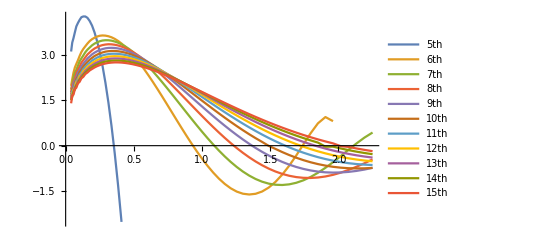

```mathematica
ListLinePlot[{
(If[#[[1]]<0.36,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[5]]),(*
(If[#[[1]]<0.55,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[6]]),
(If[#[[1]]<0.75||#[[1]]>1.3,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[7]]),*)
(If[#[[1]]<0.95||#[[1]]>1.7,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[8]]),
(If[#[[1]]<1.1||#[[1]]>2.1,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[9]]),
(If[#[[1]]<1.25||#[[1]]>2.5,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[10]]),
(If[#[[1]]<1.35,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[11]]),
(If[#[[1]]<1.45,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[12]]),
(If[#[[1]]<1.6,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[13]]),
(If[#[[1]]<1.7,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[14]]),
(If[#[[1]]<1.8,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[15]]),
(If[#[[1]]<1.9,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[16]]),
(If[#[[1]]<2,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[17]])
},PlotLegends->(*{"5","6","7","8","9","10"}*)((ToString[#]<>"th")&/@Range[5,17](*{5,8,11,14,17}*)),PlotRange->All]
```

#### Debug

```mathematica
λ=10^-4;
```

```mathematica
H1[n_][ϕ_][x_?NumberQ]:=((m1^2-β^2)/x+(m2^2-β^2)/(1-x))ϕn[n][ϕ][x]; 
H2[n_][ϕ_][x_?NumberQ]:=2 β^2(ϕn[n][ϕ][x])/λ-β^2 NIntegrate[Boole[(y>x+λ||y<x-λ)](ϕn[n][ϕ][y])/(x-y)^2,{y,0,1},PrecisionGoal->15,Method->"AdaptiveMonteCarlo",MaxPoints->10^8,MaxRecursion->30];
```

```mathematica
(*H[n_][ϕ_][x_?NumberQ]:=NIntegrate[H1[n][x]-H2[n][x]+β^2(ϕ[n][x])/λ,{x,0,1}]*)
```

```mathematica
m1=0.6;m2=m1;
```

```mathematica
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
Φ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx}]
},
{
{Vals,ϕx}=Import[dir<>filename];
Φ[x_]=ϕx;
}
];
```

```mathematica
Block[{x=1,y=1},Boole[(y>x+λ||y<x-λ)](ϕn[1][Φ][y])/(x-y)^2]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
Plot3D[Boole[(y>x+λ||y<x-λ)](ϕn[1][Φ][y])/(x-y)^2,{y,0,1},{x,0,1}]
```

```mathematica
Plot[ϕn[10][Φ][x],{x,0,1}]
```

```mathematica
Block[{x=0.3,n=1,ϕ=Φ},NIntegrate[Boole[(y>x+λ||y<x-λ)](ϕn[n][ϕ][y])/(x-y)^2,{y,0,1},PrecisionGoal->15,Method->"AdaptiveMonteCarlo",MaxPoints->10^8,MaxRecursion->30]]
```

```mathematica
Block[{x=0.3,n=1,ϕ=Φ},NIntegrate[(ϕn[n][ϕ][y])/(x-y)^2,{y,0,x-λ},PrecisionGoal->15,Method->"AdaptiveMonteCarlo",MaxPoints->10^8,MaxRecursion->30]+NIntegrate[(ϕn[n][ϕ][y])/(x-y)^2,{y,x+λ,1},PrecisionGoal->15,Method->"AdaptiveMonteCarlo",MaxPoints->10^8,MaxRecursion->30]]
```

```mathematica
H2[1][Φ][0.3]
```

```mathematica
H1[1][Φ][0.3]
```

```mathematica
(Mn[1][Vals])^2 ϕn[1][Φ][0.3]
```

```mathematica
ListPlot[Table[{x,(Mn[#][Vals])^2 ϕn[#][Φ][x]-H1[#][Φ][x]-H2[#][Φ][x]&[1]},{x,0.1,0.9,0.1}]]
```

### NIntegration Test

```mathematica
{M2,ϕ2}={Mn[#][Vals],ϕn[#][Φ]}&[1];
{M3,ϕ3}={Mn[#][Vals],ϕn[#][Φ]}&[1];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][Φ]}&[8];
```

```mathematica
temp=ω[M1,M2,M3]
```

0.813059

```mathematica
A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.813056}. NIntegrate obtained -0.0000170334 and 9.85165×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.813059}. NIntegrate obtained -0.000131412 and 0.0000287662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.813059}. NIntegrate obtained -0.0000683775 and 1.58463×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

3.53202

```mathematica
A[temp][ϕ1,ϕ2,ϕ3]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.813056}. NIntegrate obtained -0.0000170334 and 9.85165×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.813059}. NIntegrate obtained -0.000131412 and 0.0000287662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.813059}. NIntegrate obtained -0.0000683775 and 1.58463×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

3.53202

#### Part1

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp}]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp]Kernel[(x-temp)/(1-temp)],{x,0,temp}]//AbsoluteTiming
```

$Aborted

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"LocalAdaptive"]//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.813056}. NIntegrate obtained -0.0000170334 and 9.85165×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.813059}. NIntegrate obtained -0.000131412 and 0.0000287662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.813059}. NIntegrate obtained -0.0000683775 and 1.58463×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{27.2004,0.112793}

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"AdaptiveMonteCarlo",PrecisionGoal->20,MaxPoints->10^10]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"MultiPeriodic",PrecisionGoal->20]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"MonteCarloRule",PrecisionGoal->20,MaxPoints->10^9]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"NewtonCotesRule"]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"GaussBerntsenEspelidRule"]//AbsoluteTiming.
```

#### Part2

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1}]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"LocalAdaptive"]//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.999954,0.919432}. NIntegrate obtained -0.0003123 and 1.03978×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.999957,0.919432}. NIntegrate obtained -0.000351754 and 1.17428×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.999961,0.919432}. NIntegrate obtained -0.00040328 and 1.35137×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{95.5362,-13.163}

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"QuasiMonteCarlo",PrecisionGoal->20]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"AdaptiveQuasiMonteCarlo"]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"MonteCarlo",PrecisionGoal->20]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"AdaptiveMonteCarlo",AccuracyGoal->20]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"AdaptiveMonteCarlo",PrecisionGoal->20,MaxPoints->10^10]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"MultidimensionalRule"]//AbsoluteTiming
```

```mathematica
Plot3D[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{x,temp,1},{p,0,1},PlotPoints->10,MaxRecursion->0]
```

```mathematica
ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2/.{x->0.95,p->0.5}
```

#### Part3

```mathematica
1/Nc NIntegrate[ϕ3[x],{x,0,1}]NIntegrate[ϕ1[x]ϕ2[x/temp],{x,0,temp}]//AbsoluteTiming
```

```mathematica
1/Nc NIntegrate[ϕ3[x],{x,0,1}]NIntegrate[ϕ1[x]ϕ2[x/temp],{x,0,temp},Method->"LocalAdaptive"]//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00393023}. NIntegrate obtained 1.46463×10^-14 and 7.5213×10^-8 for the integral and error estimates.

{16.356,-3.45744×10^-20}

```mathematica
1/Nc NIntegrate[ϕ3[x],{x,0,1}]NIntegrate[ϕ1[x]ϕ2[x/temp],{x,0,temp},Method->"AdaptiveMonteCarlo",PrecisionGoal->20,MaxPoints->10^9]//AbsoluteTiming
```

#### Sum

```mathematica
1/(1-temp)%%%[[2]]-1/temp%%[[2]]+1/Nc 1/(1-temp)%[[2]]
```

```mathematica
1/(1-temp)%%%[[2]]-1/temp%%[[2]]
```